```mathematica
(*
This code makes the time series plots (Figures 4-6). It requires that the time series simulations have been run or you can use the uploaded time series simulations that were part of the study. 
*)
```

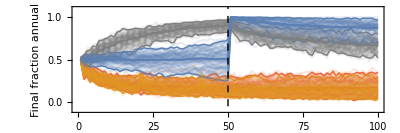

```mathematica
f1=Show[ListLinePlot[{aMat01CI,aMat1CI,aMat2CI,aMat3CI},IntervalMarkers->"Bands",PlotRange->{{0,100},{-.1,1.1}},PlotStyle->{ColorData[97,4],ColorData[97,2],Gray,ColorData[97,1]},
Frame->True,Epilog->{Black,Dashed,Thick,Line[{{50,-1},{50,2}}]},FrameLabel->{"Time","Fraction annual",None,None},
AspectRatio->1/3 ],
ListLinePlot[tsdat01,PlotStyle->Directive[{ColorData[97,4],Opacity[.15]}]],ListLinePlot[tsdat1,PlotStyle->Directive[{ColorData[97,2],Opacity[.15]}]],
ListLinePlot[tsdat2,PlotStyle->Directive[{Gray,Opacity[.15]}]],
ListLinePlot[tsdat3,PlotStyle->Directive[{ColorData[97,1],Opacity[.15]}]]
]
```

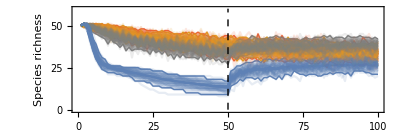

```mathematica
f2=Show[
ListLinePlot[{spdat01CI,spdat1CI,spdat2CI,spdat3CI},IntervalMarkers->"Bands",PlotRange->{{0,100},{-.4,60}},PlotStyle->{ColorData[97,4],ColorData[97,2],Gray,ColorData[97,1]}, 
Frame->True,

Epilog->{Black,Dashed,Thick,Line[{{50,0},{50,60}}]},FrameLabel->{"Time","Species richness",None,None},
AspectRatio->1/3 ],
ListLinePlot[spdat01,PlotStyle->Directive[{ColorData[97,4],Opacity[.15]}]],
ListLinePlot[spdat1,PlotStyle->Directive[{ColorData[97,2],Opacity[.15]}]],
ListLinePlot[spdat2,PlotStyle->Directive[{Gray,Opacity[.15]}]],
ListLinePlot[spdat3,PlotStyle->Directive[{ColorData[97,1],Opacity[.15]}]]]
```

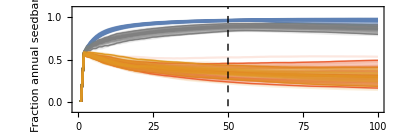

```mathematica
f3=Show[ListLinePlot[{sBlist01,sBlist3,sBlist2,sBlist1},IntervalMarkers->"Bands",PlotRange->{{0,100},{-.1,1.1}},PlotStyle->{ColorData[97,4],ColorData[97,1],Gray,ColorData[97,2]}, 
Frame->True,
Epilog->{Black,Dashed,Thick,Line[{{50,-1},{50,60}}]},FrameLabel->{"Time","Fraction annual seedbank",None,None},
AspectRatio->1/3 ],
ListLinePlot[sB01a,PlotStyle->Directive[{ColorData[97,4],Opacity[.15]}]],
ListLinePlot[sB3a,PlotStyle->Directive[{ColorData[97,1],Opacity[.15]}]],
ListLinePlot[sB2a,PlotStyle->Directive[{Gray,Opacity[.15]}]],
ListLinePlot[sB1a,PlotStyle->Directive[{ColorData[97,2],Opacity[.15]}]]
]
```

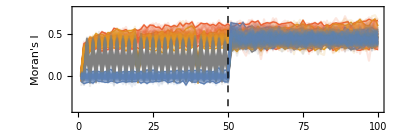

```mathematica
f4=Show[ListLinePlot[{space01CI,space3CI,space2CI,space1CI},IntervalMarkers->"Bands",PlotRange->{{0,100},{-.4,.8}},PlotStyle->{ColorData[97,4],ColorData[97,1],Gray,ColorData[97,2]}, 
Frame->True,Epilog->{Black,Dashed,Thick,Line[{{50,-1},{50,60}}]},FrameLabel->{"Time","Moran's I",None,None},
AspectRatio->1/3 ],
ListLinePlot[space01,PlotStyle->Directive[{ColorData[97,4],Opacity[.15]}]],
ListLinePlot[space1,PlotStyle->Directive[{ColorData[97,2],Opacity[.15]}]],
ListLinePlot[space2,PlotStyle->Directive[{Gray,Opacity[.15]}]],
ListLinePlot[space3,PlotStyle->Directive[{ColorData[97,1],Opacity[.15]}]]]
```

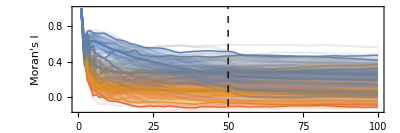

```mathematica
f5=Show[ListLinePlot[{
 Table[Around[Mean[bankMI01][[x]],{Quantile[bankMI01,0.025][[x]]-Mean[bankMI01][[x]],Mean[bankMI1][[x]]-Quantile[bankMI1,0.975][[x]]}],{x,1,100}],
Table[Around[Mean[bankMI1][[x]],{Quantile[bankMI1,0.025][[x]]-Mean[bankMI1][[x]],Mean[bankMI1][[x]]-Quantile[bankMI1,0.975][[x]]}],{x,1,100}],
Table[Around[Mean[bankMI2][[x]],{Quantile[bankMI2,0.025][[x]]-Mean[bankMI2][[x]],Mean[bankMI2][[x]]-Quantile[bankMI2,0.975][[x]]}],{x,1,100}],
Table[Around[Mean[bankMI3][[x]],{Quantile[bankMI3,0.025][[x]]-Mean[bankMI3][[x]],Mean[bankMI3][[x]]-Quantile[bankMI3,0.975][[x]]}],{x,1,100}]},PlotRange->{{-0.1,All},{-.15,All}},IntervalMarkers->"Bands",Frame->True,Epilog->{Black,Dashed,Thick,Line[{{50,-2},{50,2}}]},FrameLabel->{"Time","Moran's I",None,None},AspectRatio->1/3 ,PlotStyle->{ColorData[97,4],Directive[{ColorData[97,2]}],Directive[{Gray}],Directive[{ColorData[97,1]}]}],
ListLinePlot[bankMI01,PlotStyle->Directive[{ColorData[97,4],Opacity[.15]}]],
ListLinePlot[bankMI1,PlotStyle->Directive[{ColorData[97,2],Opacity[.15]}]],
ListLinePlot[bankMI2,PlotStyle->Directive[{Gray,Opacity[.15]}]],
ListLinePlot[bankMI3,PlotStyle->Directive[{ColorData[97,1],,Opacity[.15]}]]]
```

```mathematica
ArrayPlot[savedBank01[[4,100]],Frame->True,Axes->True,ImageSize->200, 
Epilog->{Red,Thick,Line[{{25,0},{25,100}}]}]
ArrayPlot[savedBank1[[4,100]],Frame->True,Axes->True,ImageSize->200, 
Epilog->{Red,Thick,Line[{{25,0},{25,100}}]}]
ArrayPlot[savedBank2[[4,100]],Frame->True,Axes->True,ImageSize->200, 
Epilog->{Red,Thick,Line[{{25,0},{25,100}}]}]
ArrayPlot[savedBank3[[4,100]],Frame->True,Axes->True,ImageSize->200, 
Epilog->{Red,Thick,Line[{{25,0},{25,100}}]}]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

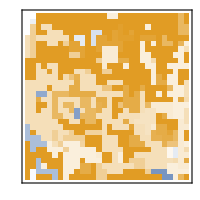

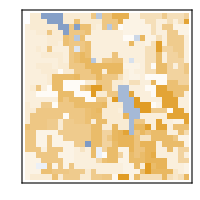

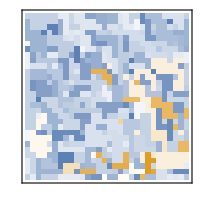

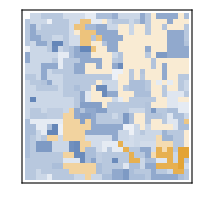

```mathematica
MatrixPlot[
aMat01[[4,All,All,100]],
ColorRules->{
1->Lighter[ColorData[97,2],.04],2->Lighter[ColorData[97,2],.08],3->Lighter[ColorData[97,2],.12],4->Lighter[ColorData[97,2],.16],5->Lighter[ColorData[97,2],.2],6->Lighter[ColorData[97,2],.24],7->Lighter[ColorData[97,2],.28],8->Lighter[ColorData[97,2],.32],9->Lighter[ColorData[97,2],.36],10->Lighter[ColorData[97,2],.4],
11->Lighter[ColorData[97,2],.44],12->Lighter[ColorData[97,2],.48],
13->Lighter[ColorData[97,2],.52],14->Lighter[ColorData[97,2],.56],
15->Lighter[ColorData[97,2],.6],16->Lighter[ColorData[97,2],.64],
17->Lighter[ColorData[97,2],.68],18->Lighter[ColorData[97,2],.72],
19->Lighter[ColorData[97,2],.76],20->Lighter[ColorData[97,2],.8],
21->Lighter[ColorData[97,2],.84],22->Lighter[ColorData[97,2],.88],
23->Lighter[ColorData[97,2],.92],24->Lighter[ColorData[97,2],.96],
25->ColorData[97,2],
26->Lighter[ColorData[97,1],.04],27->Lighter[ColorData[97,1],.08],28->Lighter[ColorData[97,1],.12],29->Lighter[ColorData[97,1],.16],30->Lighter[ColorData[97,1],.2],31->Lighter[ColorData[97,1],.24],32->Lighter[ColorData[97,1],.28],33->Lighter[ColorData[97,1],.32],34->Lighter[ColorData[97,1],.36],35->Lighter[ColorData[97,1],.4],36->Lighter[ColorData[97,1],.44],37->Lighter[ColorData[97,1],.48],38->Lighter[ColorData[97,1],.52],39->Lighter[ColorData[97,1],.56],40->Lighter[ColorData[97,1],.6],41->Lighter[ColorData[97,1],.64],42->Lighter[ColorData[97,1],.68],43->Lighter[ColorData[97,1],.72],44->Lighter[ColorData[97,1],.76],45->Lighter[ColorData[97,1],.8],46->Lighter[ColorData[97,1],.84],47->Lighter[ColorData[97,1],.88],48->Lighter[ColorData[97,1],.92],49->Lighter[ColorData[97,1],.96],50->ColorData[97,1]},
ImageSize->200,FrameTicks->False]
MatrixPlot[
aMat1[[4,All,All,100]],
ColorRules->{
1->Lighter[ColorData[97,2],.04],2->Lighter[ColorData[97,2],.08],3->Lighter[ColorData[97,2],.12],4->Lighter[ColorData[97,2],.16],5->Lighter[ColorData[97,2],.2],6->Lighter[ColorData[97,2],.24],7->Lighter[ColorData[97,2],.28],8->Lighter[ColorData[97,2],.32],9->Lighter[ColorData[97,2],.36],10->Lighter[ColorData[97,2],.4],
11->Lighter[ColorData[97,2],.44],12->Lighter[ColorData[97,2],.48],
13->Lighter[ColorData[97,2],.52],14->Lighter[ColorData[97,2],.56],
15->Lighter[ColorData[97,2],.6],16->Lighter[ColorData[97,2],.64],
17->Lighter[ColorData[97,2],.68],18->Lighter[ColorData[97,2],.72],
19->Lighter[ColorData[97,2],.76],20->Lighter[ColorData[97,2],.8],
21->Lighter[ColorData[97,2],.84],22->Lighter[ColorData[97,2],.88],
23->Lighter[ColorData[97,2],.92],24->Lighter[ColorData[97,2],.96],
25->ColorData[97,2],
26->Lighter[ColorData[97,1],.04],27->Lighter[ColorData[97,1],.08],28->Lighter[ColorData[97,1],.12],29->Lighter[ColorData[97,1],.16],30->Lighter[ColorData[97,1],.2],31->Lighter[ColorData[97,1],.24],32->Lighter[ColorData[97,1],.28],33->Lighter[ColorData[97,1],.32],34->Lighter[ColorData[97,1],.36],35->Lighter[ColorData[97,1],.4],36->Lighter[ColorData[97,1],.44],37->Lighter[ColorData[97,1],.48],38->Lighter[ColorData[97,1],.52],39->Lighter[ColorData[97,1],.56],40->Lighter[ColorData[97,1],.6],41->Lighter[ColorData[97,1],.64],42->Lighter[ColorData[97,1],.68],43->Lighter[ColorData[97,1],.72],44->Lighter[ColorData[97,1],.76],45->Lighter[ColorData[97,1],.8],46->Lighter[ColorData[97,1],.84],47->Lighter[ColorData[97,1],.88],48->Lighter[ColorData[97,1],.92],49->Lighter[ColorData[97,1],.96],50->ColorData[97,1]},
ImageSize->200,FrameTicks->False]
MatrixPlot[
aMat2[[4,All,All,100]],
ColorRules->{
1->Lighter[ColorData[97,2],.04],2->Lighter[ColorData[97,2],.08],3->Lighter[ColorData[97,2],.12],4->Lighter[ColorData[97,2],.16],5->Lighter[ColorData[97,2],.2],6->Lighter[ColorData[97,2],.24],7->Lighter[ColorData[97,2],.28],8->Lighter[ColorData[97,2],.32],9->Lighter[ColorData[97,2],.36],10->Lighter[ColorData[97,2],.4],
11->Lighter[ColorData[97,2],.44],12->Lighter[ColorData[97,2],.48],
13->Lighter[ColorData[97,2],.52],14->Lighter[ColorData[97,2],.56],
15->Lighter[ColorData[97,2],.6],16->Lighter[ColorData[97,2],.64],
17->Lighter[ColorData[97,2],.68],18->Lighter[ColorData[97,2],.72],
19->Lighter[ColorData[97,2],.76],20->Lighter[ColorData[97,2],.8],
21->Lighter[ColorData[97,2],.84],22->Lighter[ColorData[97,2],.88],
23->Lighter[ColorData[97,2],.92],24->Lighter[ColorData[97,2],.96],
25->ColorData[97,2],
26->Lighter[ColorData[97,1],.04],27->Lighter[ColorData[97,1],.08],28->Lighter[ColorData[97,1],.12],29->Lighter[ColorData[97,1],.16],30->Lighter[ColorData[97,1],.2],31->Lighter[ColorData[97,1],.24],32->Lighter[ColorData[97,1],.28],33->Lighter[ColorData[97,1],.32],34->Lighter[ColorData[97,1],.36],35->Lighter[ColorData[97,1],.4],36->Lighter[ColorData[97,1],.44],37->Lighter[ColorData[97,1],.48],38->Lighter[ColorData[97,1],.52],39->Lighter[ColorData[97,1],.56],40->Lighter[ColorData[97,1],.6],41->Lighter[ColorData[97,1],.64],42->Lighter[ColorData[97,1],.68],43->Lighter[ColorData[97,1],.72],44->Lighter[ColorData[97,1],.76],45->Lighter[ColorData[97,1],.8],46->Lighter[ColorData[97,1],.84],47->Lighter[ColorData[97,1],.88],48->Lighter[ColorData[97,1],.92],49->Lighter[ColorData[97,1],.96],50->ColorData[97,1]},
ImageSize->200,FrameTicks->False]
MatrixPlot[
aMat3[[4,All,All,100]],
ColorRules->{
1->Lighter[ColorData[97,2],.04],2->Lighter[ColorData[97,2],.08],3->Lighter[ColorData[97,2],.12],4->Lighter[ColorData[97,2],.16],5->Lighter[ColorData[97,2],.2],6->Lighter[ColorData[97,2],.24],7->Lighter[ColorData[97,2],.28],8->Lighter[ColorData[97,2],.32],9->Lighter[ColorData[97,2],.36],10->Lighter[ColorData[97,2],.4],
11->Lighter[ColorData[97,2],.44],12->Lighter[ColorData[97,2],.48],
13->Lighter[ColorData[97,2],.52],14->Lighter[ColorData[97,2],.56],
15->Lighter[ColorData[97,2],.6],16->Lighter[ColorData[97,2],.64],
17->Lighter[ColorData[97,2],.68],18->Lighter[ColorData[97,2],.72],
19->Lighter[ColorData[97,2],.76],20->Lighter[ColorData[97,2],.8],
21->Lighter[ColorData[97,2],.84],22->Lighter[ColorData[97,2],.88],
23->Lighter[ColorData[97,2],.92],24->Lighter[ColorData[97,2],.96],
25->ColorData[97,2],
26->Lighter[ColorData[97,1],.04],27->Lighter[ColorData[97,1],.08],28->Lighter[ColorData[97,1],.12],29->Lighter[ColorData[97,1],.16],30->Lighter[ColorData[97,1],.2],31->Lighter[ColorData[97,1],.24],32->Lighter[ColorData[97,1],.28],33->Lighter[ColorData[97,1],.32],34->Lighter[ColorData[97,1],.36],35->Lighter[ColorData[97,1],.4],36->Lighter[ColorData[97,1],.44],37->Lighter[ColorData[97,1],.48],38->Lighter[ColorData[97,1],.52],39->Lighter[ColorData[97,1],.56],40->Lighter[ColorData[97,1],.6],41->Lighter[ColorData[97,1],.64],42->Lighter[ColorData[97,1],.68],43->Lighter[ColorData[97,1],.72],44->Lighter[ColorData[97,1],.76],45->Lighter[ColorData[97,1],.8],46->Lighter[ColorData[97,1],.84],47->Lighter[ColorData[97,1],.88],48->Lighter[ColorData[97,1],.92],49->Lighter[ColorData[97,1],.96],50->ColorData[97,1]},
ImageSize->200,FrameTicks->False]
```

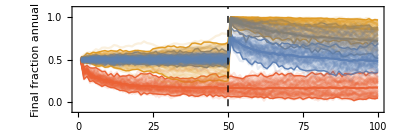

```mathematica
d1=Show[ListLinePlot[{aMat01CI,aMat1CI,aMat2CI,aMat3CI},IntervalMarkers->"Bands",PlotRange->{{0,100},{-.1,1.1}},PlotStyle->{ColorData[97,4],ColorData[97,2],Gray,ColorData[97,1]},
Frame->True,Epilog->{Black,Dashed,Thick,Line[{{50,-1},{50,2}}]},FrameLabel->{"Time","Fraction annual",None,None},
AspectRatio->1/3 ],
ListLinePlot[tsdat01,PlotStyle->Directive[{ColorData[97,4],Opacity[.15]}]],ListLinePlot[tsdat1,PlotStyle->Directive[{ColorData[97,2],Opacity[.15]}]],
ListLinePlot[tsdat2,PlotStyle->Directive[{Gray,Opacity[.15]}]],
ListLinePlot[tsdat3,PlotStyle->Directive[{ColorData[97,1],Opacity[.15]}]]
]
```

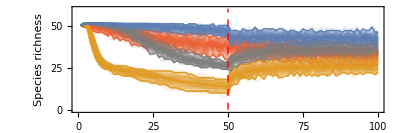

```mathematica
d2=Show[
ListLinePlot[{spdat01CI,spdat1CI,spdat2CI,spdat3CI},IntervalMarkers->"Bands",PlotRange->{{0,100},{-.4,60}},PlotStyle->{ColorData[97,4],ColorData[97,2],Gray,ColorData[97,1]}, 
Frame->True,

Epilog->{Black,Dashed,Thick,Line[{{50,0},{50,60}}]},FrameLabel->{"Time","Species richness",None,None},
AspectRatio->1/3 ],
ListLinePlot[spdat01,PlotStyle->Directive[{ColorData[97,4],Opacity[.15]}]],
ListLinePlot[spdat1,PlotStyle->Directive[{ColorData[97,2],Opacity[.15]}]],
ListLinePlot[spdat2,PlotStyle->Directive[{Gray,Opacity[.15]}]],
ListLinePlot[spdat3,PlotStyle->Directive[{ColorData[97,1],Opacity[.15]}]]]
```

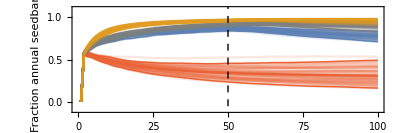

```mathematica
d3=Show[ListLinePlot[{sBlist01,sBlist3,sBlist2,sBlist1},IntervalMarkers->"Bands",PlotRange->{{0,100},{-.1,1.1}},PlotStyle->{ColorData[97,4],ColorData[97,1],Gray,ColorData[97,2]}, 
Frame->True,
Epilog->{Black,Dashed,Thick,Line[{{50,-1},{50,60}}]},FrameLabel->{"Time","Fraction annual seedbank",None,None},
AspectRatio->1/3 ],
ListLinePlot[sB01a,PlotStyle->Directive[{ColorData[97,4],Opacity[.15]}]],
ListLinePlot[sB3a,PlotStyle->Directive[{ColorData[97,1],Opacity[.15]}]],
ListLinePlot[sB2a,PlotStyle->Directive[{Gray,Opacity[.15]}]],
ListLinePlot[sB1a,PlotStyle->Directive[{ColorData[97,2],Opacity[.15]}]]
]
```

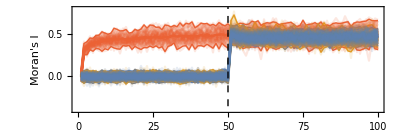

```mathematica
d4=Show[ListLinePlot[{space01CI,space3CI,space2CI,space1CI},IntervalMarkers->"Bands",PlotRange->{{0,100},{-.4,.8}},PlotStyle->{ColorData[97,4],ColorData[97,1],Gray,ColorData[97,2]}, 
Frame->True,Epilog->{Black,Dashed,Thick,Line[{{50,-1},{50,60}}]},FrameLabel->{"Time","Moran's I",None,None},
AspectRatio->1/3 ],
ListLinePlot[space01,PlotStyle->Directive[{ColorData[97,4],Opacity[.15]}]],
ListLinePlot[space1,PlotStyle->Directive[{ColorData[97,2],Opacity[.15]}]],
ListLinePlot[space2,PlotStyle->Directive[{Gray,Opacity[.15]}]],
ListLinePlot[space3,PlotStyle->Directive[{ColorData[97,1],Opacity[.15]}]]]
```

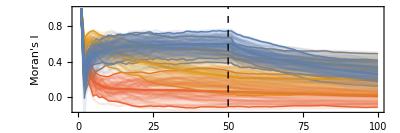

```mathematica
d5=Show[ListLinePlot[{
 Table[Around[Mean[bankMI01][[x]],{Quantile[bankMI01,0.025][[x]]-Mean[bankMI01][[x]],Mean[bankMI1][[x]]-Quantile[bankMI1,0.975][[x]]}],{x,1,100}],
Table[Around[Mean[bankMI1][[x]],{Quantile[bankMI1,0.025][[x]]-Mean[bankMI1][[x]],Mean[bankMI1][[x]]-Quantile[bankMI1,0.975][[x]]}],{x,1,100}],
Table[Around[Mean[bankMI2][[x]],{Quantile[bankMI2,0.025][[x]]-Mean[bankMI2][[x]],Mean[bankMI2][[x]]-Quantile[bankMI2,0.975][[x]]}],{x,1,100}],
Table[Around[Mean[bankMI3][[x]],{Quantile[bankMI3,0.025][[x]]-Mean[bankMI3][[x]],Mean[bankMI3][[x]]-Quantile[bankMI3,0.975][[x]]}],{x,1,100}]},PlotRange->{{-0.1,All},{-.15,All}},IntervalMarkers->"Bands",Frame->True,Epilog->{Black,Dashed,Thick,Line[{{50,-2},{50,2}}]},FrameLabel->{"Time","Moran's I",None,None},AspectRatio->1/3 ,PlotStyle->{ColorData[97,4],Directive[{ColorData[97,2]}],Directive[{Gray}],Directive[{ColorData[97,1]}]}],
ListLinePlot[bankMI01,PlotStyle->Directive[{ColorData[97,4],Opacity[.15]}]],
ListLinePlot[bankMI1,PlotStyle->Directive[{ColorData[97,2],Opacity[.15]}]],
ListLinePlot[bankMI2,PlotStyle->Directive[{Gray,Opacity[.15]}]],
ListLinePlot[bankMI3,PlotStyle->Directive[{ColorData[97,1],,Opacity[.15]}]]]
```

```mathematica
ArrayPlot[savedBank01[[4,100]],Frame->True,Axes->True,ImageSize->200, 
Epilog->{Red,Thick,Line[{{25,0},{25,100}}]}]
ArrayPlot[savedBank1[[4,100]],Frame->True,Axes->True,ImageSize->200, 
Epilog->{Red,Thick,Line[{{25,0},{25,100}}]}]
ArrayPlot[savedBank2[[4,100]],Frame->True,Axes->True,ImageSize->200, 
Epilog->{Red,Thick,Line[{{25,0},{25,100}}]}]
ArrayPlot[savedBank3[[4,100]],Frame->True,Axes->True,ImageSize->200, 
Epilog->{Red,Thick,Line[{{25,0},{25,100}}]}]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

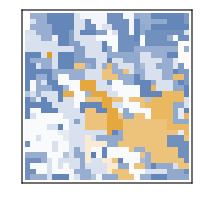

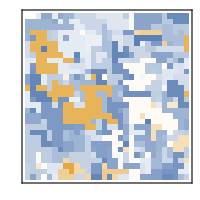

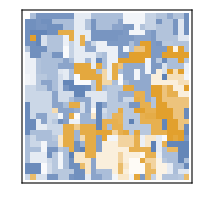

```mathematica
MatrixPlot[
aMat01[[4,All,All,100]],
ColorRules->{
1->Lighter[ColorData[97,2],.04],2->Lighter[ColorData[97,2],.08],3->Lighter[ColorData[97,2],.12],4->Lighter[ColorData[97,2],.16],5->Lighter[ColorData[97,2],.2],6->Lighter[ColorData[97,2],.24],7->Lighter[ColorData[97,2],.28],8->Lighter[ColorData[97,2],.32],9->Lighter[ColorData[97,2],.36],10->Lighter[ColorData[97,2],.4],
11->Lighter[ColorData[97,2],.44],12->Lighter[ColorData[97,2],.48],
13->Lighter[ColorData[97,2],.52],14->Lighter[ColorData[97,2],.56],
15->Lighter[ColorData[97,2],.6],16->Lighter[ColorData[97,2],.64],
17->Lighter[ColorData[97,2],.68],18->Lighter[ColorData[97,2],.72],
19->Lighter[ColorData[97,2],.76],20->Lighter[ColorData[97,2],.8],
21->Lighter[ColorData[97,2],.84],22->Lighter[ColorData[97,2],.88],
23->Lighter[ColorData[97,2],.92],24->Lighter[ColorData[97,2],.96],
25->ColorData[97,2],
26->Lighter[ColorData[97,1],.04],27->Lighter[ColorData[97,1],.08],28->Lighter[ColorData[97,1],.12],29->Lighter[ColorData[97,1],.16],30->Lighter[ColorData[97,1],.2],31->Lighter[ColorData[97,1],.24],32->Lighter[ColorData[97,1],.28],33->Lighter[ColorData[97,1],.32],34->Lighter[ColorData[97,1],.36],35->Lighter[ColorData[97,1],.4],36->Lighter[ColorData[97,1],.44],37->Lighter[ColorData[97,1],.48],38->Lighter[ColorData[97,1],.52],39->Lighter[ColorData[97,1],.56],40->Lighter[ColorData[97,1],.6],41->Lighter[ColorData[97,1],.64],42->Lighter[ColorData[97,1],.68],43->Lighter[ColorData[97,1],.72],44->Lighter[ColorData[97,1],.76],45->Lighter[ColorData[97,1],.8],46->Lighter[ColorData[97,1],.84],47->Lighter[ColorData[97,1],.88],48->Lighter[ColorData[97,1],.92],49->Lighter[ColorData[97,1],.96],50->ColorData[97,1]},
ImageSize->200,FrameTicks->False]
MatrixPlot[
aMat1[[4,All,All,100]],
ColorRules->{
1->Lighter[ColorData[97,2],.04],2->Lighter[ColorData[97,2],.08],3->Lighter[ColorData[97,2],.12],4->Lighter[ColorData[97,2],.16],5->Lighter[ColorData[97,2],.2],6->Lighter[ColorData[97,2],.24],7->Lighter[ColorData[97,2],.28],8->Lighter[ColorData[97,2],.32],9->Lighter[ColorData[97,2],.36],10->Lighter[ColorData[97,2],.4],
11->Lighter[ColorData[97,2],.44],12->Lighter[ColorData[97,2],.48],
13->Lighter[ColorData[97,2],.52],14->Lighter[ColorData[97,2],.56],
15->Lighter[ColorData[97,2],.6],16->Lighter[ColorData[97,2],.64],
17->Lighter[ColorData[97,2],.68],18->Lighter[ColorData[97,2],.72],
19->Lighter[ColorData[97,2],.76],20->Lighter[ColorData[97,2],.8],
21->Lighter[ColorData[97,2],.84],22->Lighter[ColorData[97,2],.88],
23->Lighter[ColorData[97,2],.92],24->Lighter[ColorData[97,2],.96],
25->ColorData[97,2],
26->Lighter[ColorData[97,1],.04],27->Lighter[ColorData[97,1],.08],28->Lighter[ColorData[97,1],.12],29->Lighter[ColorData[97,1],.16],30->Lighter[ColorData[97,1],.2],31->Lighter[ColorData[97,1],.24],32->Lighter[ColorData[97,1],.28],33->Lighter[ColorData[97,1],.32],34->Lighter[ColorData[97,1],.36],35->Lighter[ColorData[97,1],.4],36->Lighter[ColorData[97,1],.44],37->Lighter[ColorData[97,1],.48],38->Lighter[ColorData[97,1],.52],39->Lighter[ColorData[97,1],.56],40->Lighter[ColorData[97,1],.6],41->Lighter[ColorData[97,1],.64],42->Lighter[ColorData[97,1],.68],43->Lighter[ColorData[97,1],.72],44->Lighter[ColorData[97,1],.76],45->Lighter[ColorData[97,1],.8],46->Lighter[ColorData[97,1],.84],47->Lighter[ColorData[97,1],.88],48->Lighter[ColorData[97,1],.92],49->Lighter[ColorData[97,1],.96],50->ColorData[97,1]},
ImageSize->200,FrameTicks->False]
MatrixPlot[
aMat2[[4,All,All,100]],
ColorRules->{
1->Lighter[ColorData[97,2],.04],2->Lighter[ColorData[97,2],.08],3->Lighter[ColorData[97,2],.12],4->Lighter[ColorData[97,2],.16],5->Lighter[ColorData[97,2],.2],6->Lighter[ColorData[97,2],.24],7->Lighter[ColorData[97,2],.28],8->Lighter[ColorData[97,2],.32],9->Lighter[ColorData[97,2],.36],10->Lighter[ColorData[97,2],.4],
11->Lighter[ColorData[97,2],.44],12->Lighter[ColorData[97,2],.48],
13->Lighter[ColorData[97,2],.52],14->Lighter[ColorData[97,2],.56],
15->Lighter[ColorData[97,2],.6],16->Lighter[ColorData[97,2],.64],
17->Lighter[ColorData[97,2],.68],18->Lighter[ColorData[97,2],.72],
19->Lighter[ColorData[97,2],.76],20->Lighter[ColorData[97,2],.8],
21->Lighter[ColorData[97,2],.84],22->Lighter[ColorData[97,2],.88],
23->Lighter[ColorData[97,2],.92],24->Lighter[ColorData[97,2],.96],
25->ColorData[97,2],
26->Lighter[ColorData[97,1],.04],27->Lighter[ColorData[97,1],.08],28->Lighter[ColorData[97,1],.12],29->Lighter[ColorData[97,1],.16],30->Lighter[ColorData[97,1],.2],31->Lighter[ColorData[97,1],.24],32->Lighter[ColorData[97,1],.28],33->Lighter[ColorData[97,1],.32],34->Lighter[ColorData[97,1],.36],35->Lighter[ColorData[97,1],.4],36->Lighter[ColorData[97,1],.44],37->Lighter[ColorData[97,1],.48],38->Lighter[ColorData[97,1],.52],39->Lighter[ColorData[97,1],.56],40->Lighter[ColorData[97,1],.6],41->Lighter[ColorData[97,1],.64],42->Lighter[ColorData[97,1],.68],43->Lighter[ColorData[97,1],.72],44->Lighter[ColorData[97,1],.76],45->Lighter[ColorData[97,1],.8],46->Lighter[ColorData[97,1],.84],47->Lighter[ColorData[97,1],.88],48->Lighter[ColorData[97,1],.92],49->Lighter[ColorData[97,1],.96],50->ColorData[97,1]},
ImageSize->200,FrameTicks->False]
MatrixPlot[
aMat3[[4,All,All,100]],
ColorRules->{
1->Lighter[ColorData[97,2],.04],2->Lighter[ColorData[97,2],.08],3->Lighter[ColorData[97,2],.12],4->Lighter[ColorData[97,2],.16],5->Lighter[ColorData[97,2],.2],6->Lighter[ColorData[97,2],.24],7->Lighter[ColorData[97,2],.28],8->Lighter[ColorData[97,2],.32],9->Lighter[ColorData[97,2],.36],10->Lighter[ColorData[97,2],.4],
11->Lighter[ColorData[97,2],.44],12->Lighter[ColorData[97,2],.48],
13->Lighter[ColorData[97,2],.52],14->Lighter[ColorData[97,2],.56],
15->Lighter[ColorData[97,2],.6],16->Lighter[ColorData[97,2],.64],
17->Lighter[ColorData[97,2],.68],18->Lighter[ColorData[97,2],.72],
19->Lighter[ColorData[97,2],.76],20->Lighter[ColorData[97,2],.8],
21->Lighter[ColorData[97,2],.84],22->Lighter[ColorData[97,2],.88],
23->Lighter[ColorData[97,2],.92],24->Lighter[ColorData[97,2],.96],
25->ColorData[97,2],
26->Lighter[ColorData[97,1],.04],27->Lighter[ColorData[97,1],.08],28->Lighter[ColorData[97,1],.12],29->Lighter[ColorData[97,1],.16],30->Lighter[ColorData[97,1],.2],31->Lighter[ColorData[97,1],.24],32->Lighter[ColorData[97,1],.28],33->Lighter[ColorData[97,1],.32],34->Lighter[ColorData[97,1],.36],35->Lighter[ColorData[97,1],.4],36->Lighter[ColorData[97,1],.44],37->Lighter[ColorData[97,1],.48],38->Lighter[ColorData[97,1],.52],39->Lighter[ColorData[97,1],.56],40->Lighter[ColorData[97,1],.6],41->Lighter[ColorData[97,1],.64],42->Lighter[ColorData[97,1],.68],43->Lighter[ColorData[97,1],.72],44->Lighter[ColorData[97,1],.76],45->Lighter[ColorData[97,1],.8],46->Lighter[ColorData[97,1],.84],47->Lighter[ColorData[97,1],.88],48->Lighter[ColorData[97,1],.92],49->Lighter[ColorData[97,1],.96],50->ColorData[97,1]},
ImageSize->200,FrameTicks->False]
```